expanding  the  asymptotic  radial  S -wave wave function or its definite integral (∫_0)^x dr e^(-r/a)/(√(2π a))= ...    in a certain interval in a set of Gaussians or integrals thereof (∫_0)^x dr ce^(-ar^2)=c/2 √(π/a)Erf(√a x)

```mathematica
hbarc=197.327053;
Mm=938.858;
b2=2.22;
```

```mathematica
GaussX[x_,c_,a_]:=c Exp[-a x^2];IGaussX[x_,c_,a_]:=c/2 √(π/a) Erf[√a x];
dimerAsy[r_]:=(√((√(Mm b2))/(2 π hbarc))) Exp[-(√(Mm b2))/hbarc r];IdimerAsy[r_]:=√(hbarc/(2 π √(Mm b2))) (1-Exp[-(√(Mm b2))/hbarc r]);
```

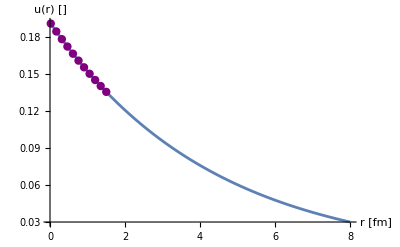

```mathematica
rMin=0;rMax=8;fitInterval=Subdivide[0.02,1.5,10];

fitData=Table[{fitInterval[[n]],dimerAsy[fitInterval[[n]]]},{n,Range[Length[fitInterval]]}];
Plot[dimerAsy[rr],{rr,rMin,rMax},AxesLabel->{"r [fm]","u(r) []"},PlotLabels->Placed["e^(-SqrtBox[m  B] r)",Above],PlotRange->Automatic,Epilog->{PointSize[0.015],Purple,Point[fitData]}]
```

u^(opt)(r) = 0.0204347 ⅇ^(-5.32732 r^2)+0.169024 ⅇ^(-0.1009 r^2)

{c_n,a_n} = {{0.0204347,5.32732},{0.169024,0.1009}}

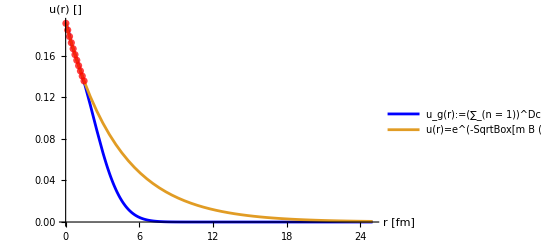

```mathematica
guassdim=2;

modelGuass=Sum[GaussX[xx,cGn@i,aGn@i],{i,guassdim}];

nlmG=NonlinearModelFit[fitData,modelGuass,Flatten[Table[{{aGn@i,RandomReal[{0.1,2.14}]},{cGn@i,RandomReal[{0.08,15.4}]}},{i,guassdim}],1],xx];
modelG[s_]:=Sum[GaussX[s,cGn@i,aGn@i],{i,guassdim}]/.nlmG["BestFitParameters"];
Print["u^(opt)(r) = ",modelG[r]];
Print["{c_n,a_n} = ",Sort[Table[{cGn@i,aGn@i},{i,guassdim}]/.nlmG["BestFitParameters"],#1[[2]]>#2[[2]]&]];
nbrS=100;
rMin=0;rMax=25;
sStellen=Subdivide[rMin,rMax,nbrS];

Show[
Plot[{modelG[sr],dimerAsy[sr]},{sr,rMin,rMax},PlotLegends->{"u_g(r):=(∑_(n = 1))^Dc_n^(opt)·e^(-SubsuperscriptBox[a, n, (opt)] SuperscriptBox[r, 2])","u(r)=e^(-SqrtBox[m  B (dimer)] r)"},PlotRange->Full,AxesLabel->{"r [fm]","u(r) []"},PlotStyle->{Blue,Thick,Dashed,Opacity[0.75]}],
ListPlot[fitData,PlotStyle->{Red,Opacity[0.75]}]
]
CoeffWidthSet=Sort[Table[{cGn@i,aGn@i},{i,guassdim}]/.nlmG["BestFitParameters"],#1[[2]]>#2[[2]]&];
Put[CoeffWidthSet,"UnivDimerWF"]
```

vizualization of the probability density that results from the Gaussians which have been choosen to approximate the wave function directly
cf to the graph below which fits directly to the density.

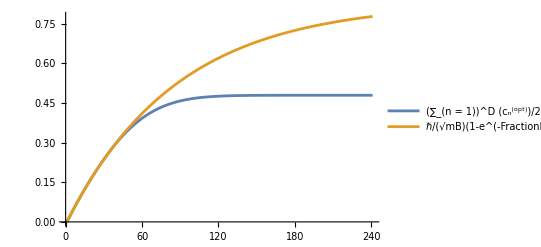

```mathematica
rR=Range[0,12,0.05];
modeltmp[s_]:=Total[IGaussX[s,#[[1]],#[[2]]]&/@CoeffWidthSet];
IGaussXTab=Table[modeltmp[rr],{rr,rR}];
IdimerAsyTab=Table[IdimerAsy[rr],{rr,rR}];

(*Plot[IdimerAsy[rr],{rr,rMin,rMax},AxesLabel->{"x [fm]","(∫_0)^xdru(r)"},PlotLabels->Placed["ℏ/(√mB)(1-e^(-FractionBox[SqrtBox[m B], ℏ]r))",Above],PlotRange->All,Epilog->{PointSize[0.015],Purple,Point[fitData]}]*)
ListPlot[{IGaussXTab,IdimerAsyTab},PlotLegends->{"(∑_(n = 1))^D c_n^(opt)/2√(π/a_n)Erf[√a_n x]","ℏ/(√mB)(1-e^(-FractionBox[SqrtBox[m  B], ℏ] r))"},Joined->True,PlotRange->Full]
```

direct fit to density

NonlinearModelFit::nrlnum: The function value {-3.34529,-1.51594×10^29,-3.43857×10^97,-2.1631×10^205,-3.33125581347976×10^352+0. ⅈ,-1.20281547739835×10^539+0. ⅈ,-9.97866419308235×10^764+0. ⅈ,-1.88106888407559×10^1030+0. ⅈ,-8.00309715767036×10^1334+0. ⅈ,-7.65084971122065×10^1678+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-67.3673,7.52248,-2.47572,-9.48252}.

NonlinearModelFit::nrlnum: The function value {-2.88586×10^17,-4.20438564084861×10^470+0. ⅈ,-2.35566588973838×10^1534+0. ⅈ,-2.21509894189142×10^3208+0. ⅈ,-3.09504147157325×10^5492+0. ⅈ,-6.15690406660632×10^8386+0. ⅈ,-1.70905680881707×10^11891+0. ⅈ,-6.54703690102657×10^16005+0. ⅈ,-3.43793680276865×10^20730+0. ⅈ,-2.46375219434391×10^26065+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1044.67,84.755,-18.6688,-105.493}.

NonlinearModelFit::nrlnum: The function value {-1.65848×10^73,-8.39597226190256×10^1909+0. ⅈ,-1.11236532147109×10^6217+0. ⅈ,-1.69768301054067×10^12994+0. ⅈ,-2.64295307640674×10^22241+0. ⅈ,-4.0214700808883×10^33958+0. ⅈ,-5.86166738971958×10^48145+0. ⅈ,-8.09460063078377×10^64802+0. ⅈ,-1.05191022281266×10^83930+0. ⅈ,-1.28071459047359×10^105527+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-4229.11,954.08,-73.8331,-1063.69}.

NonlinearModelFit::nrlnum: The function value {2.53727×10^13,2.03705638253964×10^338+0. ⅈ,2.45532580986244×10^1101+0. ⅈ,1.92989846348437×10^2302+0. ⅈ,8.75730339124563×10^3940+0. ⅈ,2.19806366026431×10^6017+0. ⅈ,2.99101263065829×10^8531+0. ⅈ,2.18222632930022×10^11483+0. ⅈ,8.47920829509641×10^14872+0. ⅈ,1.74689136150015×10^18700+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-749.467,-714.553,-413.747,686.498}.

NonlinearModelFit::nrlnum: The function value {-1.94058×10^23,-1.54170316084502×10^645+0. ⅈ,-3.13354779808951×10^2104+0. ⅈ,-7.13328706090844×10^4400+0. ⅈ,-1.6103121180367×10^7534+0. ⅈ,-3.45405886509822×10^11504+0. ⅈ,-6.89962278552208×10^16311+0. ⅈ,-1.26938464913735×10^21956+0. ⅈ,-2.13650644442501×10^28437+0. ⅈ,-3.27521296339057×10^35755+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {2909.83,11.6381,-1433.04,14.0566}.

NonlinearModelFit::nrlnum: The function value {-5.31889,-1.48737×10^18,-5.75474×10^59,-2.77388×10^125,-1.4672×10^215,-8.1530766718335×10^328+0. ⅈ,-4.66413195688308×10^466+0. ⅈ,-2.71643585918567×10^628+0. ⅈ,-1.59979309990691×10^814+0. ⅈ,-9.48501848446805×10^1023+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1.90563,-38.6578,-41.0871,33.5532}.

NonlinearModelFit::nrlnum: The function value {-1.81494×10^89,-4.99176105791415×10^2335+0. ⅈ,-2.21963007290442×10^7603+0. ⅈ,-7.02714343610152×10^15891+0. ⅈ,-1.40263063075056×10^27201+0. ⅈ,-1.69127239807291×10^41531+0. ⅈ,-1.20744709833369×10^58882+0. ⅈ,-5.04782182847242×10^79253+0. ⅈ,-1.22741767085096×10^102646+0. ⅈ,-1.72828207332339×10^129059+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-76.502,-591.255,-5172.18,529.129}.

NonlinearModelFit::nrlnum: The function value {-43.8487,-9.76754×10^16,-3.29898×10^52,-4.6634×10^108,-2.42859×10^185,-4.4603×10^282,-2.83073451733301×10^400+0. ⅈ,-6.13928866388056×10^538+0. ⅈ,-4.51933275972469×10^697+0. ⅈ,-1.12419322681899×10^877+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-27.0887,-916.342,-35.1387,916.47}.

NonlinearModelFit::nrlnum: The function value {-135.367,-2.80049×10^25,-1.42692×10^81,-1.12787×10^169,-1.21986×10^289,-1.72876544651391×10^441+0. ⅈ,-3.14589411118377×10^625+0. ⅈ,-7.26953061637883×10^841+0. ⅈ,-2.11876624235655×10^1090+0. ⅈ,-7.75443604786691×10^1370+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-54.9491,462.091,-10.9572,-462.098}.

NonlinearModelFit::nrlnum: The function value {-4.77729×10^64,-2.96789713579072×10^1710+0. ⅈ,-1.12016453560804×10^5570+0. ⅈ,-1.1302124129071×10^11643+0. ⅈ,-2.69943017093642×10^19929+0. ⅈ,-1.46236692728944×10^30429+0. ⅈ,-1.76112890510852×10^43142+0. ⅈ,-4.66308584245858×10^58068+0. ⅈ,-2.69633720655802×10^75208+0. ⅈ,-3.38980688473457×10^94561+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-7.86487,-134.28,-3789.7,105.839}.

NonlinearModelFit::nrlnum: The function value {705.771,4.04543×10^17,1.66611×10^54,1.2051×10^112,1.34734×10^191,2.22898×10^291,5.34665266810948×10^412+0. ⅈ,1.83892432315432×10^555+0. ⅈ,9.00753626827156×10^718+0. ⅈ,6.25578387808669×10^903+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-36.2051,-1289.72,4.3743,1290.42}.

NonlinearModelFit::nrlnum: The function value {2.08044×10^7,1.07404×10^181,4.95604185131528×10^589+0. ⅈ,8.74329875949576×10^1232+0. ⅈ,5.21946889676171×10^2110+0. ⅈ,1.01017101240439×10^3223+0. ⅈ,6.21227684781306×10^4569+0. ⅈ,1.20057100811011×10^6151+0. ⅈ,7.24228742274694×10^7966+0. ⅈ,1.35767332582763×10^10017+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {13026.3,361.341,-401.49,-342.376}.

NonlinearModelFit::nrlnum: The function value {-8.93789×10^26,-2.5561875823329×10^759+0. ⅈ,-7.71326546913167×10^2477+0. ⅈ,-1.07638947060912×10^5182+0. ⅈ,-6.15098849035165×10^8871+0. ⅈ,-1.37910876529034×10^13547+0. ⅈ,-1.18906962342986×10^19208+0. ⅈ,-3.89912986626603×10^25854+0. ⅈ,-4.83003879636201×10^33486+0. ⅈ,-2.25028421443186×10^42104+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1687.5,2.89937,2210.59,0.172233}.

NonlinearModelFit::nrlnum: The function value {346014.,4.68824×10^116,4.46492037020323×10^378+0. ⅈ,1.25331540323172×10^791+0. ⅈ,9.17503551825025×10^1353+0. ⅈ,1.67819731475381×10^2067+0. ⅈ,7.51675723156237×10^2930+0. ⅈ,8.15383938440633×10^3944+0. ⅈ,2.12768223692745×10^5109+0. ⅈ,1.32967261924279×10^6424+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-46.9173,1157.86,-257.47,-1135.27}.

NonlinearModelFit::nrlnum: The function value {-2.73344×10^9,-4.56794×10^246,-1.58043579010199×10^804+0. ⅈ,-4.88624004964212×10^1681+0. ⅈ,-1.19498132905023×10^2879+0. ⅈ,-2.21489013436583×10^4396+0. ⅈ,-3.04944136605326×10^6233+0. ⅈ,-3.08432534340006×10^8390+0. ⅈ,-2.27636542810532×10^10867+0. ⅈ,-1.22052491734527×10^13664+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-15.1911,-229.746,-547.66,179.02}.

NonlinearModelFit::nrlnum: The function value {5.58385×10^6,4.31408×10^150,2.45129006733537×10^489+0. ⅈ,4.34909571863964×10^1022+0. ⅈ,2.13225865420736×10^1750+0. ⅈ,2.76768799126572×10^2672+0. ⅈ,9.3217711171027×10^3788+0. ⅈ,8.05706605746924×10^5099+0. ⅈ,1.77509659255211×10^6605+0. ⅈ,9.9246282874399×10^8304+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {642.395,1202.43,-332.851,-1176.99}.

NonlinearModelFit::nrlnum: The function value {-0.207798,-4.21985×10^13,-2.00371×10^49,-4.84306×10^105,-5.2436×10^182,-2.43442×10^280,-4.74884633841187×10^398+0. ⅈ,-3.84913580391693×10^537+0. ⅈ,-1.28758353706875×10^697+0. ⅈ,-1.76969214129709×10^877+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-35.284,0.341693,0.647713,-0.252179}.

NonlinearModelFit::nrlnum: The function value {2.04802×10^10,3.53477×10^251,3.13981203084954×10^818+0. ⅈ,6.19770816322683×10^1710+0. ⅈ,2.40654053640952×10^2928+0. ⅈ,1.76119168348732×10^4471+0. ⅈ,2.38091479687093×10^6339+0. ⅈ,5.88030259328989×10^8532+0. ⅈ,2.63538587545962×10^11051+0. ⅈ,2.13382326840142×10^13895+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-556.898,-942.951,1600.11,971.712}.

NonlinearModelFit::nrlnum: The function value {-4.56066,-3.23059×10^21,-2.9408×10^72,-7.8718×10^152,-5.46312×10^262,-9.4128936447377×10^401+0. ⅈ,-3.94568215977521×10^570+0. ⅈ,-3.97930610753418×10^768+0. ⅈ,-9.59042904515101×10^995+0. ⅈ,-5.49907638674822×10^1252+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {0.356987,-7.84395,-50.2877,6.22496}.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::nrlnum: The function value {-8.21085×10^26,-1.14684689871176×10^752+0. ⅈ,-2.51050495059805×10^2453+0. ⅈ,-3.77504255339394×10^5130+0. ⅈ,-3.45259724112426×10^8783+0. ⅈ,-1.8402084471848×10^13412+0. ⅈ,-5.60224582279095×10^19016+0. ⅈ,-9.63446989250053×10^25596+0. ⅈ,-9.29682930143532×10^33152+0. ⅈ,-5.01146372678774×10^41684+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1670.68,5.16894,2808.52,189.236}.

NonlinearModelFit::nrlnum: The function value {-1.1049×10^15,-1.48468991909545×10^377+0. ⅈ,-3.25829907737356×10^1227+0. ⅈ,-5.08141128138602×10^2565+0. ⅈ,-4.9856267826694×10^4391+0. ⅈ,-2.94864483357788×10^6705+0. ⅈ,-1.03030818413425×10^9507+0. ⅈ,-2.10353365178109×10^12796+0. ⅈ,-2.49252713875298×10^16573+0. ⅈ,-1.70655227855528×10^20838+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-84.2816,-1178.82,-835.141,1128.46}.

NonlinearModelFit::nrlnum: The function value {4.00443×10^12,1.69100492785252×10^312+0. ⅈ,1.12220937194821×10^1016+0. ⅈ,5.07641608485913×10^2123+0. ⅈ,1.38572154315953×10^3635+0. ⅈ,2.18701572001153×10^5550+0. ⅈ,1.95595456360111×10^7869+0. ⅈ,9.80374118068437×10^10591+0. ⅈ,2.73540393505931×10^13718+0. ⅈ,4.22988666426118×10^17248+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {619.818,1093.05,-691.284,-1064.56}.

NonlinearModelFit::nrlnum: The function value {-9.33507×10^18,-1.97108549270242×10^486+0. ⅈ,-1.73866929156555×10^1583+0. ⅈ,-2.79698842610863×10^3309+0. ⅈ,-7.2653203417218×10^5664+0. ⅈ,-2.91970083082698×10^8649+0. ⅈ,-1.77916884232477×10^12263+0. ⅈ,-1.62587525306496×10^16506+0. ⅈ,-2.21319241457353×10^21378+0. ⅈ,-4.467805452365×10^26879+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1077.26,767.9,-86.745,-774.16}.

NonlinearModelFit::nrlnum: The function value {-2.48742×10^50,-1.49150588463152×10^1366+0. ⅈ,-1.28420720081442×10^4452+0. ⅈ,-6.98109945277363×10^9307+0. ⅈ,-2.1216495280134×10^15933+0. ⅈ,-3.45399806454061×10^24328+0. ⅈ,-2.95220968357708×10^34493+0. ⅈ,-1.31022484843059×10^46428+0. ⅈ,-2.99908652407159×10^60132+0. ⅈ,-3.52499172785401×10^75606+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-3030.11,6.9028,1863.15,15.7779}.

NonlinearModelFit::nrlnum: The function value {401.736,135341.,1.49832×10^12,3.48464×10^23,1.43858×10^39,1.00493×10^59,1.16271×10^83,2.20258×10^111,6.78429×10^143,3.38242×10^180,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {11.7161,1020.98,-7.19584,-1020.29}.

NonlinearModelFit::nrlnum: The function value {605.022,7.91519×10^31,2.29286×10^101,7.93577×10^210,2.89696180774468×10^360+0. ⅈ,1.06824817794217×10^550+0. ⅈ,3.89942038811067×10^779+0. ⅈ,1.39348824203585×10^1049+0. ⅈ,4.84221715237946×10^1358+0. ⅈ,1.6289212238051×10^1708+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-15.2993,1290.24,-68.4534,-1289.43}.

NonlinearModelFit::nrlnum: The function value {-2.20341468028614×10^539+0. ⅈ,-1.90051460819197×10^14061+0. ⅈ,-4.42554093798729×10^45761+0. ⅈ,-1.22750517368167×10^95640+0. ⅈ,-3.59129913717021×10^163696+0. ⅈ,-1.06192256204289×10^249931+0. ⅈ,-3.11047216360237×10^354343+0. ⅈ,-8.9258434217709×10^476933+0. ⅈ,-2.49248685155784×10^617702+0. ⅈ,-6.74308529106476×10^776648+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-31124.6,560.558,-72.8047,-658.815}.

NonlinearModelFit::nrlnum: The function value {-0.356009,-34940.2,-6.08348×10^14,-1.45651×10^31,-4.1388×10^53,-1.33286×10^82,-4.76352×10^116,-1.86796×10^157,-7.98198×10^203,-3.70008×10^256,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-10.3227,15.1128,-1.01726,-15.6704}.

NonlinearModelFit::nrlnum: The function value {173.703,5.16332×10^23,5.71564×10^74,2.08129×10^155,2.19821×10^265,6.44809740789623×10^404+0. ⅈ,5.14779833165232×10^573+0. ⅈ,1.10613633240182×10^772+0. ⅈ,6.35407214757326×10^999+0. ⅈ,9.71465937050724×10^1256+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-23.7571,914.097,-50.3711,-913.747}.

NonlinearModelFit::nrlnum: The function value {0.447589,1057.39,1.17021×10^8,1.79215×10^16,3.39213×10^27,7.54622×10^41,1.93023×10^59,5.61079×10^79,1.84045×10^103,6.7816×10^129,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1.48033,47.3717,-5.21196,-47.2495}.

NonlinearModelFit::nrlnum: The function value {-7.00245×10^44,-6.19638458517835×10^1162+0. ⅈ,-9.12319744663813×10^3784+0. ⅈ,-9.8202653683832×10^7910+0. ⅈ,-6.84296042646422×10^13540+0. ⅈ,-2.95764600459145×10^20674+0. ⅈ,-7.77154799311792×10^29311+0. ⅈ,-1.22779206789692×10^39453+0. ⅈ,-1.15842798240569×10^51098+0. ⅈ,-6.49862646915089×10^64246+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-2574.77,1341.36,-55.0906,-1357.46}.

NonlinearModelFit::nrlnum: The function value {-53608.1,-9.77302×10^109,-1.56942350122414×10^358+0. ⅈ,-9.39894876528497×10^748+0. ⅈ,-1.85730997636823×10^1282+0. ⅈ,-1.16021798135314×10^1958+0. ⅈ,-2.24547588922249×10^2776+0. ⅈ,-1.33162639390777×10^3737+0. ⅈ,-2.4034235812954×10^4840+0. ⅈ,-1.31441485155042×10^6086+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-117.367,-291.924,-243.948,288.921}.

NonlinearModelFit::nrlnum: The function value {1.11896×10^37,2.01680747968043×10^966+0. ⅈ,1.3563222191887×10^3146+0. ⅈ,1.49401739147254×10^6576+0. ⅈ,2.38678251716897×10^11256+0. ⅈ,5.29870879848165×10^17186+0. ⅈ,1.60215592415846×10^24367+0. ⅈ,6.52549849098943×10^32797+0. ⅈ,3.55604888466503×10^42478+0. ⅈ,2.58135798165636×10^53409+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-2140.47,-623.805,1387.11,672.033}.

NonlinearModelFit::nrlnum: The function value {-2.65488×10^6,-1.38996×10^156,-3.67240859983314×10^508+0. ⅈ,-2.08280543365728×10^1063+0. ⅈ,-2.24411588625074×10^1820+0. ⅈ,-4.40090554138921×10^2779+0. ⅈ,-1.53959747623476×10^3941+0. ⅈ,-9.50241500551483×10^5304+0. ⅈ,-1.02776049699885×10^6871+0. ⅈ,-1.93937424478774×10^8639+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-346.27,341.039,-83.8804,-356.558}.

NonlinearModelFit::nrlnum: The function value {-2.05798×10^19,-8.19938125609811×10^534+0. ⅈ,-1.06954814504356×10^1745+0. ⅈ,-1.99616885519698×10^3649+0. ⅈ,-4.71963071886453×10^6247+0. ⅈ,-1.35444966913858×10^9540+0. ⅈ,-4.62421379318771×10^13526+0. ⅈ,-1.85750187333759×10^18207+0. ⅈ,-8.7198224302178×10^23581+0. ⅈ,-4.76271183203837×10^29650+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {13503.3,58.9193,-1188.38,21.9544}.

NonlinearModelFit::nrlnum: The function value {1.14344085451498×10^349+0. ⅈ,5.42467467451758×10^9104+0. ⅈ,5.48247831947805×10^29631+0. ⅈ,5.20688471574207×10^61929+0. ⅈ,4.11514077571021×10^105998+0. ⅈ,2.59321553895636×10^161838+0. ⅈ,1.2770821592658×10^229449+0. ⅈ,4.86096629860764×10^308830+0. ⅈ,1.42043417924878×10^399983+0. ⅈ,3.17245771872257×10^502906+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-20154.3,-706.411,-5.27559,720.564}.

NonlinearModelFit::nrlnum: The function value {-4.60713×10^72,-1.14638962741559×10^1900+0. ⅈ,-2.29114738802938×10^6185+0. ⅈ,-1.61884104682439×10^12928+0. ⅈ,-3.58077185484608×10^22128+0. ⅈ,-2.37579624838378×10^33786+0. ⅈ,-4.63425819739888×10^47901+0. ⅈ,-2.6283714357606×10^64474+0. ⅈ,-4.30526408340162×10^83504+0. ⅈ,-2.02768662417299×10^104992+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-78.2185,-690.16,-4207.68,621.273}.

NonlinearModelFit::nrlnum: The function value {-0.605379,-1.08968×10^43,-1.54516×10^146,-5.43981439211388×10^308+0. ⅈ,-4.20173646689447×10^530+0. ⅈ,-6.82041452631331×10^811+0. ⅈ,-2.28019091255085×10^1152+0. ⅈ,-1.55272185225958×10^1552+0. ⅈ,-2.13916053309993×10^2011+0. ⅈ,-5.93606884493419×10^2529+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-101.53,0.29923,0.615931,-0.271207}.

NonlinearModelFit::nrlnum: The function value {-6.48013025533891×10^740+0. ⅈ,-6.69208769046872×10^19323+0. ⅈ,-4.86804209125304×10^62888+0. ⅈ,-1.10064433147526×10^131435+0. ⅈ,-6.84935863908969×10^224962+0. ⅈ,-1.12409987890313×10^343472+0. ⅈ,-4.76860340493481×10^486962+0. ⅈ,-5.17137580924326×10^655434+0. ⅈ,-1.42403539497725×10^848888+0. ⅈ,-9.91326597925812×10^1067322+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-42773.5,98.4114,-6.92904,-139.787}.

NonlinearModelFit::nrlnum: The function value {-2.75614×10^18,-1.08413793242027×10^472+0. ⅈ,-6.23298553854901×10^1536+0. ⅈ,-2.28573041009289×10^3212+0. ⅈ,-4.73365828132998×10^5498+0. ⅈ,-5.30445155711654×10^8395+0. ⅈ,-3.15232792670593×10^11903+0. ⅈ,-9.82574728319556×10^16021+0. ⅈ,-1.59556213871978×10^20751+0. ⅈ,-1.34386923270724×10^26091+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1045.66,778.685,-94.1385,-853.543}.

NonlinearModelFit::nrlnum: The function value {208703.,2.20478×10^117,2.59654204890572×10^381+0. ⅈ,1.42757857455693×10^797+0. ⅈ,3.24220289727817×10^1364+0. ⅈ,2.9140934491828×10^2083+0. ⅈ,1.01590790361654×10^2954+0. ⅈ,1.35857843755925×10^3976+0. ⅈ,6.92250836922125×10^5149+0. ⅈ,1.33804592439791×10^6475+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {55.9729,648.731,-259.525,-634.953}.

NonlinearModelFit::nrlnum: The function value {111.254,2.2347×10^14,2.60126×10^43,2.50388×10^89,1.75112×10^152,8.51589×10^231,2.82161969637968×10^328+0. ⅈ,6.29896968375435×10^441+0. ⅈ,9.41007980311791×10^571+0. ⅈ,9.36571613309214×10^718+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-8.18377,1259.29,-28.7946,-1259.02}.

NonlinearModelFit::nrlnum: The function value {-2.50039×10^194,-6.09355598012199×10^5125+0. ⅈ,-4.49507046627151×10^16687+0. ⅈ,-4.42555542557473×10^34879+0. ⅈ,-5.14954722863398×10^59701+0. ⅈ,-6.78549030105105×10^91153+0. ⅈ,-9.92392152499056×10^129235+0. ⅈ,-1.59320807808905×10^173948+0. ⅈ,-2.78881642568947×10^225290+0. ⅈ,-5.29916066598999×10^283262+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {1521.59,26.1382,-11352.,7.07535}.

NonlinearModelFit::nrlnum: The function value {-1.06262×10^127,-4.70192934466941×10^3360+0. ⅈ,-3.89556071318543×10^10942+0. ⅈ,-2.66313408209146×10^22872+0. ⅈ,-1.33028741159734×10^39150+0. ⅈ,-4.65229897468481×10^59775+0. ⅈ,-1.11644730955049×10^84749+0. ⅈ,-1.8182535928642×10^114070+0. ⅈ,-1.99612353742856×10^147739+0. ⅈ,-1.47068134491167×10^185756+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-7444.4,15.0349,2019.81,54.5489}.

NonlinearModelFit::nrlnum: The function value {-4.985×10^6,-3.81239×10^163,-6.26478727147622×10^532+0. ⅈ,-9.42598515213422×10^1113+0. ⅈ,-1.14926626702012×10^1907+0. ⅈ,-1.08790565089536×10^2912+0. ⅈ,-7.83622981215923×10^4128+0. ⅈ,-4.24777907152678×10^5557+0. ⅈ,-1.72117506938885×10^7198+0. ⅈ,-5.19011800294755×10^9050+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-362.759,347.56,-15.4585,-381.421}.

NonlinearModelFit::nrlnum: The function value {-4.10786×10^9,-4.70465×10^238,-1.18493828472584×10^777+0. ⅈ,-2.83038231845729×10^1624+0. ⅈ,-5.67565745539235×10^2780+0. ⅈ,-9.15428449568229×10^4245+0. ⅈ,-1.16397008877519×10^6020+0. ⅈ,-1.15388651392979×10^8103+0. ⅈ,-8.85846156741086×10^10494+0. ⅈ,-5.24334447288253×10^13195+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-528.87,550.377,-79.3581,-571.346}.

NonlinearModelFit::nrlnum: The function value {-1.07274×10^21,-5.38880427980592×10^536+0. ⅈ,-1.21026329824495×10^1747+0. ⅈ,-5.31074435483238×10^3651+0. ⅈ,-4.03139314241175×10^6250+0. ⅈ,-5.07235261042456×10^9543+0. ⅈ,-1.03679840520662×10^13531+0. ⅈ,-3.40491242644228×10^18212+0. ⅈ,-1.78449369179506×10^23588+0. ⅈ,-1.4859451915359×10^29658+0. ⅈ,«6»} is not a list of real numbers with dimensions {16} at {aGn[1],cGn[1],aGn[2],cGn[2]} = {-1188.61,1134.06,-61.7409,-1132.97}.

{c_n,a_n} = {{0.0875605,0.159053},{0.0841116,0.0152572}}

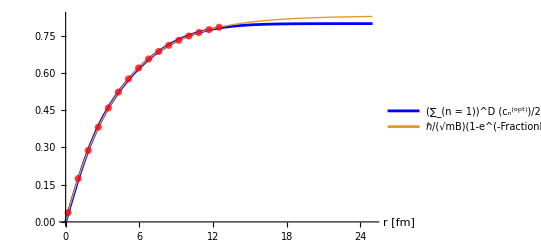

```mathematica
fitIntervalI=Subdivide[0.2,12.5,15];
fitData=Table[{fitIntervalI[[n]],IdimerAsy[fitIntervalI[[n]]]},{n,Range[Length[fitIntervalI]]}];

guassdim=2;

modelIGuass=Sum[IGaussX[xx,cGn@i,aGn@i],{i,guassdim}];

allpos=False;
While[allpos==False,
nlmIG=NonlinearModelFit[fitData,modelIGuass,Flatten[Table[{{aGn@i,RandomReal[{0.1,12.14}]},{cGn@i,RandomReal[{0.08,15.4}]}},{i,guassdim}],1],xx];
allpos=AllTrue[nlmIG["ParameterTableEntries"][[All,1]][[;;;;1]],#>0&];
]

modelIG[s_]:=Sum[IGaussX[s,cGn@i,aGn@i],{i,guassdim}]/.nlmIG["BestFitParameters"];
Print["{c_n,a_n} = ",Sort[Table[{cGn@i,aGn@i},{i,guassdim}]/.nlmIG["BestFitParameters"],#1[[2]]>#2[[2]]&]];
nbrS=100;
rMin=0;rMax=25;
sStellen=Subdivide[rMin,rMax,nbrS];

Show[
Plot[{modelIG[sr],IdimerAsy[sr]},{sr,rMin,rMax},PlotLegends->{"(∑_(n = 1))^D c_n^(opt)/2√(π/a_n)Erf[√a_n r]","ℏ/(√mB)(1-e^(-FractionBox[SqrtBox[m  B], ℏ] r))"},PlotRange->Full,AxesLabel->{"r [fm]",""},PlotStyle->{Blue,Thick,Dashed,Opacity[0.75]}],
ListPlot[fitData,PlotStyle->{Red,Opacity[0.75]}]
]
Put[Sort[Table[{cGn@i,aGn@i},{i,guassdim}]/.nlmIG["BestFitParameters"],#1[[2]]>#2[[2]]&],"UnivDimerWFI"]
```